```mathematica
ClearAll["Global`*"]
```

Faisal Muhammad g202210460

## Problem statement

Consider a tapered cantilever beam subjected to a uniform load, q  = 1 MPa.

-Graphics-

Find the optimum cross-section profile  h(x) that minimizes the beam weight (volume), taking into consideration the following constraints:
a) h_1⩾  0.01 m.
b) h_2 ≤ 2 m.
c) free end deflection ≤ 0.01 m.
Assume E = 40 GPa and ν = 0.3.

Solution

## Approach

We followed a computational intensive method in solving the problem. We wrote  a mathematica function (LinearTaperedBeam, ConvexBeam etc) with a loop that generates different values of h1 and h2 with different curves connecting the two points. From this function we calculated the values of deflection and area while checking if the values are less than the minimum (deflection ~ 0.01m). Then we used an array to store the values of the area, and utilized the inbuilt Min function and a loop to get the lowest area which will lead us to the desired geometry. As a result over ~1500 geometries was generated and compared in our project.  We got an optimal area of 5.275 m^2. The values of the geometry for which this optimal area is obtained is shown below:
-Graphics-

## Formulation

## Basic Structural Mechanics Solution

```mathematica
ClearAll["Global`*"]
```

```mathematica
hx = h1 + (h2-h1) x /L
```

h1+((-h1+h2) x)/L

```mathematica
Mx = (q x^2)/2
```

(q x^2)/2

```mathematica
II = (hx)^3/12
```

1/12 (h1+((-h1+h2) x)/L)^3

```mathematica
s = Integrate[Mx/EE, x] + C1
```

C1+(q x^3)/(6 EE)

```mathematica
v = Integrate[s, x] + C2
```

C2+C1 x+(q x^4)/(24 EE)

```mathematica
vx = D[v, x]
```

C1+(q x^3)/(6 EE)

```mathematica
bc1 = vx == 0  /. x -> L
```

C1+(L^3 q)/(6 EE)==0

```mathematica
bc2 = v == 0 /. x -> L
```

C2+C1 L+(L^4 q)/(24 EE)==0

```mathematica
sol = Solve[{bc1, bc2}, {C1, C2}]
```

{{C1→-(L^3 q)/(6 EE),C2→(L^4 q)/(8 EE)}}

```mathematica
v = Simplify[v /. sol[[1]]]
```

(q (3 L^4-4 L^3 x+x^4))/(24 EE)

## Convex Taperness

### Simple Calculation Example

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
E1 = 40*10^9; ν1 = 0.3;
```

```mathematica
q = 1*10^6;  (* in MPa *)
```

```mathematica
(* Assumed values of h1 and h2 *)
```

```mathematica
h1 = 0.01; h2 = 2;
```

```mathematica
r  = 5;
```

```mathematica
yEllipse = h2-h1;
```

```mathematica
a1 = Rectangle[{0, 0}, {r, h2}]
```

Rectangle[{0,0},{5,2}]

```mathematica
a2 = Disk[{0, 0}, {r, yEllipse}]
```

Disk[{0,0},{5,1.99}]

```mathematica
taper = RegionDifference[a1, a2]
```

BooleanRegion[#1&&!#2&,{Rectangle[{0,0},{5,2}],Disk[{0,0},{5,1.99}]}]

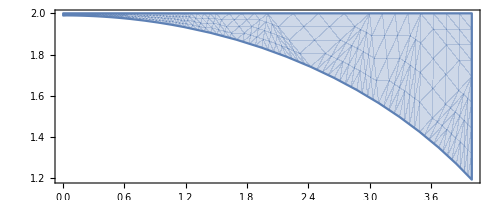

```mathematica
RegionPlot[taper, AspectRatio-> True]
```

```mathematica
r/(h2*1000.)
```

0.0025

```mathematica
mesh1 = ToElementMesh[taper, MaxCellMeasure -> r/(h2*1000.)]
```

ElementMesh[{{0.,5.},{0.,2.}},{TriangleElement[<1449>]}]

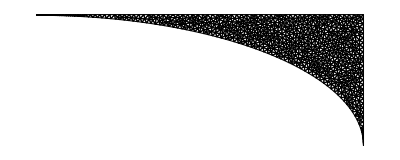

```mathematica
mesh1["Wireframe"]
```

```mathematica
PlaneStressOperator[u_,v_,EE_,ν_]:={({{0,-(EE ν)/(1-ν^2)},{-(EE (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-EE/(1-ν^2),0},{0,-(EE (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(EE (1-ν))/(2 (1-ν^2))},{-(EE ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(EE (1-ν))/(2 (1-ν^2)),0},{0,-EE/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
```

```mathematica
Dbc={DirichletCondition[v[x,y]==0,x==r && 0 ≤ y ≤ h2],DirichletCondition[u[x,y]==0,x==r&& 0≤y≤h2]};
```

```mathematica
Sbc={0,NeumannValue[-q,y==h2]};
```

```mathematica
{u1,v1}=NDSolveValue[{PlaneStressOperator[u,v,E1,ν1]==Sbc,Dbc},{u,v},{x,y}∈mesh1]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

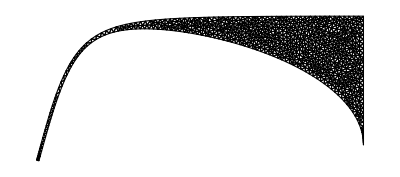

```mathematica
(* To visualize the deformed shape *)
ElementMeshDeformation[mesh1,{u1,v1}]["Wireframe"]
```

```mathematica
h1
```

0.01

```mathematica
v1[0, h2]  (* This exceeds a free end deflection of 0.01m *)
```

-2.23658

```mathematica
area = Area[taper]
```

2.18529

```mathematica
val = If[-v1[0, h2] > 0.01, "This exceeds a free end deflection of 0.01m", "Satisfactory"]
```

This exceeds a free end deflection of 0.01m

## Computational Solution

```mathematica
(* generating a list of values between the given maximum and minimum *)
```

```mathematica
(* generating a random list of h1 values *)
```

```mathematica
h1 = Range[0.01, 2.01, 0.1]
```

{0.01,0.11,0.21,0.31,0.41,0.51,0.61,0.71,0.81,0.91,1.01,1.11,1.21,1.31,1.41,1.51,1.61,1.71,1.81,1.91,2.01}

```mathematica
(* generating a random list of h2 values *)
h2 = Range[2, 0.01, -0.1]
```

{2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1}

```mathematica
lessThan = {};  (* This array will store areas values of geometry with deflection less than 0.01m. *)
greaterThan = {}; (* This array will store areas values of geometry with deflection greater than 0.01m. *)
(* The function below is responsible for generating geometries, calculating deflection, area and providing a print output for different values of h1 and h2 *)
ConvexTaperedBeam[h1_, h2_] := (
For[i= 1, i < Dimensions[h1][[1]], i++, yEllipse = h2-h1[[i]];
(* Convex Geometry *)
a1 = Rectangle[{0, 0}, {r, h2}];
a2 = Disk[{0, 0}, {r, yEllipse}];
taper = RegionDifference[a1, a2];
reg= RegionPlot[taper, AspectRatio->1];
mesh1 = ToElementMesh[taper, MaxCellMeasure -> r/(h2*1000.)];
mesho= mesh1["Wireframe"];
Dbc={DirichletCondition[v[x,y]==0,x==r && 0 ≤ y ≤ h2],DirichletCondition[u[x,y]==0,x==r&& 0≤y≤h2]};
Sbc={0,NeumannValue[-q,y==h2]};
PlaneStressOperator[u_,v_,EE_,ν_]:={({{0,-(EE ν)/(1-ν^2)},{-(EE (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-EE/(1-ν^2),0},{0,-(EE (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(EE (1-ν))/(2 (1-ν^2))},{-(EE ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(EE (1-ν))/(2 (1-ν^2)),0},{0,-EE/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
{u1,v1}=NDSolveValue[{PlaneStressOperator[u,v,E1,ν1]==Sbc,Dbc},{u,v},{x,y}∈mesh1];
(* deflection at the free-end *)
v1[0, h2] ;
status = If[-v1[0, h2] > 0.01, "Greater than 0.01m", "Less than 0.01m"];
area = Area[taper];
If [-v1[0, h2] > 0.01, greaterThan=Append[greaterThan, area], lessThan=Append[lessThan, area]];
    Print["Convex Geometry", "\n", "\n", "h1: ",h1[[i]],"m,  ", "h2: ", h2, "m ", "\n","Free-End Deflection: ", -v1[0, h2] , "\n","Status: ", status,"\n","Area: ", area,"m^2.", "\n", "\n", "--------------------------------------------------------------------------", "\n", "\n"];];
Return[];
)
```

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[1]]]]
```

Convex Geometry

h1: 0.01m,  h2: 2.m 
Free-End Deflection: 2.23658
Status: Greater than 0.01m
Area: 2.18529m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 2.m 
Free-End Deflection: 0.166885
Status: Greater than 0.01m
Area: 2.57799m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 2.m 
Free-End Deflection: 0.0773899
Status: Greater than 0.01m
Area: 2.97069m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 2.m 
Free-End Deflection: 0.0475738
Status: Greater than 0.01m
Area: 3.36339m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 2.m 
Free-End Deflection: 0.0330957
Status: Greater than 0.01m
Area: 3.75608m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 2.m 
Free-End Deflection: 0.0247085
Status: Greater than 0.01m
Area: 4.14878m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 2.m 
Free-End Deflection: 0.0193183
Status: Greater than 0.01m
Area: 4.54148m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 2.m 
Free-End Deflection: 0.015608
Status: Greater than 0.01m
Area: 4.93418m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 2.m 
Free-End Deflection: 0.0129263
Status: Greater than 0.01m
Area: 5.32688m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 2.m 
Free-End Deflection: 0.010916
Status: Greater than 0.01m
Area: 5.71958m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 2.m 
Free-End Deflection: 0.00936592
Status: Less than 0.01m
Area: 6.11228m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 2.m 
Free-End Deflection: 0.00814348
Status: Less than 0.01m
Area: 6.50498m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 2.m 
Free-End Deflection: 0.00716165
Status: Less than 0.01m
Area: 6.89768m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 2.m 
Free-End Deflection: 0.00636112
Status: Less than 0.01m
Area: 7.29038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 2.m 
Free-End Deflection: 0.00570016
Status: Less than 0.01m
Area: 7.68308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 2.m 
Free-End Deflection: 0.00514871
Status: Less than 0.01m
Area: 8.07577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 2.m 
Free-End Deflection: 0.00468463
Status: Less than 0.01m
Area: 8.46847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 2.m 
Free-End Deflection: 0.00429137
Status: Less than 0.01m
Area: 8.86117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 2.m 
Free-End Deflection: 0.00395617
Status: Less than 0.01m
Area: 9.25387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 2.m 
Free-End Deflection: 0.00367048
Status: Less than 0.01m
Area: 9.64657m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[2]]]]
```

Convex Geometry

h1: 0.01m,  h2: 1.9m 
Free-End Deflection: 2.47177
Status: Greater than 0.01m
Area: 2.07799m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 1.9m 
Free-End Deflection: 0.182611
Status: Greater than 0.01m
Area: 2.47069m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 1.9m 
Free-End Deflection: 0.0842456
Status: Greater than 0.01m
Area: 2.86339m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 1.9m 
Free-End Deflection: 0.0515956
Status: Greater than 0.01m
Area: 3.25608m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 1.9m 
Free-End Deflection: 0.0357884
Status: Greater than 0.01m
Area: 3.64878m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 1.9m 
Free-End Deflection: 0.0266546
Status: Greater than 0.01m
Area: 4.04148m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 1.9m 
Free-End Deflection: 0.0207977
Status: Greater than 0.01m
Area: 4.43418m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 1.9m 
Free-End Deflection: 0.0167745
Status: Greater than 0.01m
Area: 4.82688m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 1.9m 
Free-End Deflection: 0.0138721
Status: Greater than 0.01m
Area: 5.21958m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 1.9m 
Free-End Deflection: 0.0117004
Status: Greater than 0.01m
Area: 5.61228m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 1.9m 
Free-End Deflection: 0.0100287
Status: Greater than 0.01m
Area: 6.00498m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 1.9m 
Free-End Deflection: 0.00871257
Status: Less than 0.01m
Area: 6.39768m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 1.9m 
Free-End Deflection: 0.00765727
Status: Less than 0.01m
Area: 6.79038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 1.9m 
Free-End Deflection: 0.0067983
Status: Less than 0.01m
Area: 7.18308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 1.9m 
Free-End Deflection: 0.00609039
Status: Less than 0.01m
Area: 7.57577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 1.9m 
Free-End Deflection: 0.00550095
Status: Less than 0.01m
Area: 7.96847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 1.9m 
Free-End Deflection: 0.00500612
Status: Less than 0.01m
Area: 8.36117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 1.9m 
Free-End Deflection: 0.00458777
Status: Less than 0.01m
Area: 8.75387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 1.9m 
Free-End Deflection: 0.00423374
Status: Less than 0.01m
Area: 9.14657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 1.9m 
Free-End Deflection: 0.00423374
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.9}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[3]]]]
```

Convex Geometry

h1: 0.01m,  h2: 1.8m 
Free-End Deflection: 2.74616
Status: Greater than 0.01m
Area: 1.97069m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 1.8m 
Free-End Deflection: 0.20077
Status: Greater than 0.01m
Area: 2.36339m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 1.8m 
Free-End Deflection: 0.0921204
Status: Greater than 0.01m
Area: 2.75608m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 1.8m 
Free-End Deflection: 0.0561986
Status: Greater than 0.01m
Area: 3.14878m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 1.8m 
Free-End Deflection: 0.038862
Status: Greater than 0.01m
Area: 3.54148m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 1.8m 
Free-End Deflection: 0.0288713
Status: Greater than 0.01m
Area: 3.93418m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 1.8m 
Free-End Deflection: 0.0224804
Status: Greater than 0.01m
Area: 4.32688m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 1.8m 
Free-End Deflection: 0.0180997
Status: Greater than 0.01m
Area: 4.71958m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 1.8m 
Free-End Deflection: 0.0149459
Status: Greater than 0.01m
Area: 5.11228m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 1.8m 
Free-End Deflection: 0.0125905
Status: Greater than 0.01m
Area: 5.50498m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 1.8m 
Free-End Deflection: 0.0107807
Status: Greater than 0.01m
Area: 5.89768m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 1.8m 
Free-End Deflection: 0.00935848
Status: Less than 0.01m
Area: 6.29038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 1.8m 
Free-End Deflection: 0.00822018
Status: Less than 0.01m
Area: 6.68308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 1.8m 
Free-End Deflection: 0.00729541
Status: Less than 0.01m
Area: 7.07577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 1.8m 
Free-End Deflection: 0.00653484
Status: Less than 0.01m
Area: 7.46847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 1.8m 
Free-End Deflection: 0.00590305
Status: Less than 0.01m
Area: 7.86117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 1.8m 
Free-End Deflection: 0.00537406
Status: Less than 0.01m
Area: 8.25387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 1.8m 
Free-End Deflection: 0.00492988
Status: Less than 0.01m
Area: 8.64657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 1.8m 
Free-End Deflection: 0.00492988
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.8}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 1.8m 
Free-End Deflection: 0.00492988
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.8}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[4]]]]
```

Convex Geometry

h1: 0.01m,  h2: 1.7m 
Free-End Deflection: 3.06916
Status: Greater than 0.01m
Area: 1.86339m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 1.7m 
Free-End Deflection: Indeterminate
Status: If[Indeterminate>0.01,Greater than 0.01m,Less than 0.01m]
Area: 2.25608m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 1.7m 
Free-End Deflection: 0.101233
Status: Greater than 0.01m
Area: 2.64878m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 1.7m 
Free-End Deflection: 0.0615048
Status: Greater than 0.01m
Area: 3.04148m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 1.7m 
Free-End Deflection: 0.0423952
Status: Greater than 0.01m
Area: 3.43418m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 1.7m 
Free-End Deflection: 0.0314142
Status: Greater than 0.01m
Area: 3.82688m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 1.7m 
Free-End Deflection: 0.0244074
Status: Greater than 0.01m
Area: 4.21958m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 1.7m 
Free-End Deflection: 0.0196157
Status: Greater than 0.01m
Area: 4.61228m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 1.7m 
Free-End Deflection: 0.0161733
Status: Greater than 0.01m
Area: 5.00498m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 1.7m 
Free-End Deflection: 0.0136076
Status: Greater than 0.01m
Area: 5.39768m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 1.7m 
Free-End Deflection: 0.0116401
Status: Greater than 0.01m
Area: 5.79038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 1.7m 
Free-End Deflection: 0.010097
Status: Greater than 0.01m
Area: 6.18308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 1.7m 
Free-End Deflection: 0.00886436
Status: Less than 0.01m
Area: 6.57577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 1.7m 
Free-End Deflection: 0.00786514
Status: Less than 0.01m
Area: 6.96847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 1.7m 
Free-End Deflection: 0.00704531
Status: Less than 0.01m
Area: 7.36117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 1.7m 
Free-End Deflection: 0.00636622
Status: Less than 0.01m
Area: 7.75387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 1.7m 
Free-End Deflection: 0.00580121
Status: Less than 0.01m
Area: 8.14657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 1.7m 
Free-End Deflection: 0.00580121
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.7}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 1.7m 
Free-End Deflection: 0.00580121
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.7}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 1.7m 
Free-End Deflection: 0.00580121
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.7}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[5]]]]
```

Convex Geometry

h1: 0.01m,  h2: 1.6m 
Free-End Deflection: Indeterminate
Status: If[Indeterminate>0.01,Greater than 0.01m,Less than 0.01m]
Area: 1.75608m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 1.6m 
Free-End Deflection: 0.246702
Status: Greater than 0.01m
Area: 2.14878m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 1.6m 
Free-End Deflection: 0.111864
Status: Greater than 0.01m
Area: 2.54148m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 1.6m 
Free-End Deflection: 0.0676706
Status: Greater than 0.01m
Area: 2.93418m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 1.6m 
Free-End Deflection: 0.0464886
Status: Greater than 0.01m
Area: 3.32688m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 1.6m 
Free-End Deflection: 0.0343537
Status: Greater than 0.01m
Area: 3.71958m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 1.6m 
Free-End Deflection: 0.0266313
Status: Greater than 0.01m
Area: 4.11228m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 1.6m 
Free-End Deflection: 0.0213632
Status: Greater than 0.01m
Area: 4.50498m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 1.6m 
Free-End Deflection: 0.0175872
Status: Greater than 0.01m
Area: 4.89768m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 1.6m 
Free-End Deflection: 0.0147789
Status: Greater than 0.01m
Area: 5.29038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 1.6m 
Free-End Deflection: 0.0126301
Status: Greater than 0.01m
Area: 5.68308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 1.6m 
Free-End Deflection: 0.0109482
Status: Greater than 0.01m
Area: 6.07577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 1.6m 
Free-End Deflection: 0.0096079
Status: Less than 0.01m
Area: 6.46847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 1.6m 
Free-End Deflection: 0.00852404
Status: Less than 0.01m
Area: 6.86117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 1.6m 
Free-End Deflection: 0.00763732
Status: Less than 0.01m
Area: 7.25387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 1.6m 
Free-End Deflection: 0.00690733
Status: Less than 0.01m
Area: 7.64657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 1.6m 
Free-End Deflection: 0.00690733
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.6}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 1.6m 
Free-End Deflection: 0.00690733
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.6}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 1.6m 
Free-End Deflection: 0.00690733
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.6}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 1.6m 
Free-End Deflection: 0.00690733
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.6}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[6]]]]
```

Convex Geometry

h1: 0.01m,  h2: 1.5m 
Free-End Deflection: 3.91428
Status: Greater than 0.01m
Area: 1.64878m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 1.5m 
Free-End Deflection: 0.276092
Status: Greater than 0.01m
Area: 2.04148m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 1.5m 
Free-End Deflection: 0.124382
Status: Greater than 0.01m
Area: 2.43418m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 1.5m 
Free-End Deflection: 0.0748995
Status: Greater than 0.01m
Area: 2.82688m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 1.5m 
Free-End Deflection: 0.0512729
Status: Greater than 0.01m
Area: 3.21958m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 1.5m 
Free-End Deflection: 0.0377812
Status: Greater than 0.01m
Area: 3.61228m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 1.5m 
Free-End Deflection: 0.0292201
Status: Greater than 0.01m
Area: 4.00498m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 1.5m 
Free-End Deflection: 0.0233951
Status: Greater than 0.01m
Area: 4.39768m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 1.5m 
Free-End Deflection: 0.0192301
Status: Greater than 0.01m
Area: 4.79038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 1.5m 
Free-End Deflection: 0.0161399
Status: Greater than 0.01m
Area: 5.18308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 1.5m 
Free-End Deflection: 0.0137808
Status: Greater than 0.01m
Area: 5.57577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 1.5m 
Free-End Deflection: 0.0119388
Status: Greater than 0.01m
Area: 5.96847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 1.5m 
Free-End Deflection: 0.0104746
Status: Greater than 0.01m
Area: 6.36117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 1.5m 
Free-End Deflection: 0.00929414
Status: Less than 0.01m
Area: 6.75387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 1.5m 
Free-End Deflection: 0.00833415
Status: Less than 0.01m
Area: 7.14657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 1.5m 
Free-End Deflection: 0.00833415
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.5}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 1.5m 
Free-End Deflection: 0.00833415
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.5}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 1.5m 
Free-End Deflection: 0.00833415
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.5}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 1.5m 
Free-End Deflection: 0.00833415
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.5}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 1.5m 
Free-End Deflection: 0.00833415
Status: Less than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.5}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[7]]]]
```

Convex Geometry

h1: 0.01m,  h2: 1.4m 
Free-End Deflection: 4.47615
Status: Greater than 0.01m
Area: 1.54148m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 1.4m 
Free-End Deflection: 0.311302
Status: Greater than 0.01m
Area: 1.93418m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 1.4m 
Free-End Deflection: 0.139275
Status: Greater than 0.01m
Area: 2.32688m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 1.4m 
Free-End Deflection: 0.0834607
Status: Greater than 0.01m
Area: 2.71958m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 1.4m 
Free-End Deflection: 0.0569201
Status: Greater than 0.01m
Area: 3.11228m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 1.4m 
Free-End Deflection: 0.0418172
Status: Greater than 0.01m
Area: 3.50498m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 1.4m 
Free-End Deflection: 0.0322632
Status: Greater than 0.01m
Area: 3.89768m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 1.4m 
Free-End Deflection: 0.0257809
Status: Greater than 0.01m
Area: 4.29038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 1.4m 
Free-End Deflection: 0.0211582
Status: Greater than 0.01m
Area: 4.68308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 1.4m 
Free-End Deflection: 0.0177373
Status: Greater than 0.01m
Area: 5.07577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 1.4m 
Free-End Deflection: 0.0151324
Status: Greater than 0.01m
Area: 5.46847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 1.4m 
Free-End Deflection: 0.0131042
Status: Greater than 0.01m
Area: 5.86117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 1.4m 
Free-End Deflection: 0.0114967
Status: Greater than 0.01m
Area: 6.25387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 1.4m 
Free-End Deflection: 0.0102083
Status: Greater than 0.01m
Area: 6.64657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 1.4m 
Free-End Deflection: 0.0102083
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.4}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 1.4m 
Free-End Deflection: 0.0102083
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.4}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 1.4m 
Free-End Deflection: 0.0102083
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.4}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 1.4m 
Free-End Deflection: 0.0102083
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.4}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 1.4m 
Free-End Deflection: 0.0102083
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.4}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 1.4m 
Free-End Deflection: 0.0102083
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.4}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[8]]]]
```

Convex Geometry

h1: 0.01m,  h2: 1.3m 
Free-End Deflection: 5.1678
Status: Greater than 0.01m
Area: 1.43418m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 1.3m 
Free-End Deflection: 0.354006
Status: Greater than 0.01m
Area: 1.82688m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 1.3m 
Free-End Deflection: 0.157205
Status: Greater than 0.01m
Area: 2.21958m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 1.3m 
Free-End Deflection: 0.0937166
Status: Greater than 0.01m
Area: 2.61228m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 1.3m 
Free-End Deflection: 0.0636614
Status: Greater than 0.01m
Area: 3.00498m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 1.3m 
Free-End Deflection: 0.0466228
Status: Greater than 0.01m
Area: 3.39768m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 1.3m 
Free-End Deflection: 0.0358803
Status: Greater than 0.01m
Area: 3.79038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 1.3m 
Free-End Deflection: 0.0286137
Status: Greater than 0.01m
Area: 4.18308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 1.3m 
Free-End Deflection: 0.0234468
Status: Greater than 0.01m
Area: 4.57577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 1.3m 
Free-End Deflection: 0.0196339
Status: Greater than 0.01m
Area: 4.96847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 1.3m 
Free-End Deflection: 0.0167392
Status: Greater than 0.01m
Area: 5.36117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 1.3m 
Free-End Deflection: 0.0144923
Status: Greater than 0.01m
Area: 5.75387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 1.3m 
Free-End Deflection: 0.0127222
Status: Greater than 0.01m
Area: 6.14657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 1.3m 
Free-End Deflection: 0.0127222
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 1.3m 
Free-End Deflection: 0.0127222
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 1.3m 
Free-End Deflection: 0.0127222
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 1.3m 
Free-End Deflection: 0.0127222
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 1.3m 
Free-End Deflection: 0.0127222
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 1.3m 
Free-End Deflection: 0.0127222
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 1.3m 
Free-End Deflection: 0.0127222
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.61}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[9]]]]
```

Convex Geometry

h1: 0.01m,  h2: 1.2m 
Free-End Deflection: 6.03321
Status: Greater than 0.01m
Area: 1.32688m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 1.2m 
Free-End Deflection: 0.406543
Status: Greater than 0.01m
Area: 1.71958m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 1.2m 
Free-End Deflection: 0.179084
Status: Greater than 0.01m
Area: 2.11228m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 1.2m 
Free-End Deflection: 0.106165
Status: Greater than 0.01m
Area: 2.50498m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 1.2m 
Free-End Deflection: 0.0718133
Status: Greater than 0.01m
Area: 2.89768m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 1.2m 
Free-End Deflection: 0.0524186
Status: Greater than 0.01m
Area: 3.29038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 1.2m 
Free-End Deflection: 0.0402348
Status: Greater than 0.01m
Area: 3.68308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 1.2m 
Free-End Deflection: 0.0320209
Status: Greater than 0.01m
Area: 4.07577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 1.2m 
Free-End Deflection: 0.026199
Status: Greater than 0.01m
Area: 4.46847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 1.2m 
Free-End Deflection: 0.0219169
Status: Greater than 0.01m
Area: 4.86117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 1.2m 
Free-End Deflection: 0.0186764
Status: Greater than 0.01m
Area: 5.25387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 1.2m 
Free-End Deflection: 0.0161761
Status: Greater than 0.01m
Area: 5.64657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 1.2m 
Free-End Deflection: 0.0161761
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 1.2m 
Free-End Deflection: 0.0161761
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 1.2m 
Free-End Deflection: 0.0161761
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 1.2m 
Free-End Deflection: 0.0161761
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 1.2m 
Free-End Deflection: 0.0161761
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 1.2m 
Free-End Deflection: 0.0161761
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 1.2m 
Free-End Deflection: 0.0161761
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.61}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 1.2m 
Free-End Deflection: 0.0161761
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.71}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[10]]]]
```

Convex Geometry

h1: 0.01m,  h2: 1.1m 
Free-End Deflection: 7.13917
Status: Greater than 0.01m
Area: 1.21958m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 1.1m 
Free-End Deflection: 0.472252
Status: Greater than 0.01m
Area: 1.61228m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 1.1m 
Free-End Deflection: 0.206206
Status: Greater than 0.01m
Area: 2.00498m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 1.1m 
Free-End Deflection: 0.121509
Status: Greater than 0.01m
Area: 2.39768m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 1.1m 
Free-End Deflection: 0.0818211
Status: Greater than 0.01m
Area: 2.79038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 1.1m 
Free-End Deflection: 0.0595142
Status: Greater than 0.01m
Area: 3.18308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 1.1m 
Free-End Deflection: 0.0455567
Status: Greater than 0.01m
Area: 3.57577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 1.1m 
Free-End Deflection: 0.036182
Status: Greater than 0.01m
Area: 3.96847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 1.1m 
Free-End Deflection: 0.0295612
Status: Greater than 0.01m
Area: 4.36117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 1.1m 
Free-End Deflection: 0.024709
Status: Greater than 0.01m
Area: 4.75387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 1.1m 
Free-End Deflection: 0.0210594
Status: Greater than 0.01m
Area: 5.14657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 1.1m 
Free-End Deflection: 0.0210594
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 1.1m 
Free-End Deflection: 0.0210594
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 1.1m 
Free-End Deflection: 0.0210594
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 1.1m 
Free-End Deflection: 0.0210594
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 1.1m 
Free-End Deflection: 0.0210594
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 1.1m 
Free-End Deflection: 0.0210594
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 1.1m 
Free-End Deflection: 0.0210594
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.61}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 1.1m 
Free-End Deflection: 0.0210594
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.71}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 1.1m 
Free-End Deflection: 0.0210594
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.81}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[11]]]]
```

Convex Geometry

h1: 0.01m,  h2: 1.m 
Free-End Deflection: 8.58179
Status: Greater than 0.01m
Area: 1.11228m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 1.m 
Free-End Deflection: 0.556044
Status: Greater than 0.01m
Area: 1.50498m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 1.m 
Free-End Deflection: 0.240455
Status: Greater than 0.01m
Area: 1.89768m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 1.m 
Free-End Deflection: 0.140763
Status: Greater than 0.01m
Area: 2.29038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 1.m 
Free-End Deflection: 0.0943252
Status: Greater than 0.01m
Area: 2.68308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 1.m 
Free-End Deflection: 0.0683541
Status: Greater than 0.01m
Area: 3.07577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 1.m 
Free-End Deflection: 0.052176
Status: Greater than 0.01m
Area: 3.46847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 1.m 
Free-End Deflection: 0.0413547
Status: Greater than 0.01m
Area: 3.86117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 1.m 
Free-End Deflection: 0.0337439
Status: Greater than 0.01m
Area: 4.25387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 1.m 
Free-End Deflection: 0.0281999
Status: Greater than 0.01m
Area: 4.64657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 1.m 
Free-End Deflection: 0.0281999
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 1.m 
Free-End Deflection: 0.0281999
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 1.m 
Free-End Deflection: 0.0281999
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 1.m 
Free-End Deflection: 0.0281999
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 1.m 
Free-End Deflection: 0.0281999
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 1.m 
Free-End Deflection: 0.0281999
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 1.m 
Free-End Deflection: 0.0281999
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.61}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 1.m 
Free-End Deflection: 0.0281999
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.71}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 1.m 
Free-End Deflection: 0.0281999
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.81}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 1.m 
Free-End Deflection: 0.0281999
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.91}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[12]]]]
```

Convex Geometry

h1: 0.01m,  h2: 0.9m 
Free-End Deflection: 10.513
Status: Greater than 0.01m
Area: 1.00498m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 0.9m 
Free-End Deflection: 0.665408
Status: Greater than 0.01m
Area: 1.39768m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 0.9m 
Free-End Deflection: 0.284668
Status: Greater than 0.01m
Area: 1.79038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 0.9m 
Free-End Deflection: 0.165449
Status: Greater than 0.01m
Area: 2.18308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 0.9m 
Free-End Deflection: 0.110283
Status: Greater than 0.01m
Area: 2.57577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 0.9m 
Free-End Deflection: 0.0796024
Status: Greater than 0.01m
Area: 2.96847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 0.9m 
Free-End Deflection: 0.0605862
Status: Greater than 0.01m
Area: 3.36117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 0.9m 
Free-End Deflection: 0.0479272
Status: Greater than 0.01m
Area: 3.75387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 0.9m 
Free-End Deflection: 0.039081
Status: Greater than 0.01m
Area: 4.14657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 0.9m 
Free-End Deflection: 0.039081
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 0.9m 
Free-End Deflection: 0.039081
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 0.9m 
Free-End Deflection: 0.039081
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 0.9m 
Free-End Deflection: 0.039081
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 0.9m 
Free-End Deflection: 0.039081
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 0.9m 
Free-End Deflection: 0.039081
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 0.9m 
Free-End Deflection: 0.039081
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.61}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 0.9m 
Free-End Deflection: 0.039081
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.71}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 0.9m 
Free-End Deflection: 0.039081
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.81}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 0.9m 
Free-End Deflection: 0.039081
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.91}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 0.9m 
Free-End Deflection: 0.039081
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-1.01}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[13]]]]
```

Convex Geometry

h1: 0.01m,  h2: 0.8m 
Free-End Deflection: 13.184
Status: Greater than 0.01m
Area: 0.897677m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 0.8m 
Free-End Deflection: 0.812213
Status: Greater than 0.01m
Area: 1.29038m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 0.8m 
Free-End Deflection: 0.343295
Status: Greater than 0.01m
Area: 1.68308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 0.8m 
Free-End Deflection: 0.197932
Status: Greater than 0.01m
Area: 2.07577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 0.8m 
Free-End Deflection: 0.131179
Status: Greater than 0.01m
Area: 2.46847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 0.8m 
Free-End Deflection: 0.0942884
Status: Greater than 0.01m
Area: 2.86117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 0.8m 
Free-End Deflection: 0.0715544
Status: Greater than 0.01m
Area: 3.25387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: 3.64657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.61}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.71}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.81}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.91}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-1.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 0.8m 
Free-End Deflection: 0.056526
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-1.11}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[14]]]]
```

Convex Geometry

h1: 0.01m,  h2: 0.7m 
Free-End Deflection: 17.0272
Status: Greater than 0.01m
Area: 0.790376m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 0.7m 
Free-End Deflection: 1.01628
Status: Greater than 0.01m
Area: 1.18308m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 0.7m 
Free-End Deflection: 0.423661
Status: Greater than 0.01m
Area: 1.57577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 0.7m 
Free-End Deflection: 0.242089
Status: Greater than 0.01m
Area: 1.96847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 0.7m 
Free-End Deflection: 0.159431
Status: Greater than 0.01m
Area: 2.36117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 0.7m 
Free-End Deflection: 0.114088
Status: Greater than 0.01m
Area: 2.75387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: 3.14657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.61}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.71}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.81}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.91}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-1.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-1.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 0.7m 
Free-End Deflection: 0.0863674
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-1.21}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[15]]]]
```

Convex Geometry

h1: 0.01m,  h2: 0.6m 
Free-End Deflection: 22.8582
Status: Greater than 0.01m
Area: 0.683075m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 0.6m 
Free-End Deflection: 1.31299
Status: Greater than 0.01m
Area: 1.07577m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 0.6m 
Free-End Deflection: 0.538606
Status: Greater than 0.01m
Area: 1.46847m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 0.6m 
Free-End Deflection: 0.304631
Status: Greater than 0.01m
Area: 1.86117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 0.6m 
Free-End Deflection: 0.199217
Status: Greater than 0.01m
Area: 2.25387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: 2.64657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.61}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.71}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.81}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.91}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-1.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-1.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-1.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 0.6m 
Free-End Deflection: 0.141977
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-1.31}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[16]]]]
```

Convex Geometry

h1: 0.01m,  h2: 0.5m 
Free-End Deflection: 32.3199
Status: Greater than 0.01m
Area: 0.575775m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 0.5m 
Free-End Deflection: 1.77076
Status: Greater than 0.01m
Area: 0.968474m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 0.5m 
Free-End Deflection: 0.712636
Status: Greater than 0.01m
Area: 1.36117m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 0.5m 
Free-End Deflection: 0.398335
Status: Greater than 0.01m
Area: 1.75387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: 2.14657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.61}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.71}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.81}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.91}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-1.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-1.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-1.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-1.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 0.5m 
Free-End Deflection: 0.258563
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-1.41}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[17]]]]
```

Convex Geometry

h1: 0.01m,  h2: 0.4m 
Free-End Deflection: 49.2313
Status: Greater than 0.01m
Area: 0.468474m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 0.4m 
Free-End Deflection: 2.53807
Status: Greater than 0.01m
Area: 0.861173m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 0.4m 
Free-End Deflection: 0.997547
Status: Greater than 0.01m
Area: 1.25387m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: 1.64657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.61}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.71}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.81}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.91}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-1.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-1.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-1.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-1.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-1.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 0.4m 
Free-End Deflection: 0.550013
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-1.51}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[18]]]]
```

Convex Geometry

h1: 0.01m,  h2: 0.3m 
Free-End Deflection: 84.3096
Status: Greater than 0.01m
Area: 0.361173m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 0.3m 
Free-End Deflection: 3.99514
Status: Greater than 0.01m
Area: 0.753872m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: 1.14657m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.61}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.71}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.81}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.91}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 0.3m 
Free-End Deflection: 1.52392
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.61}]]]m^2.

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, ConvexTaperedBeam[h1, h2[[19]]]]
```

Convex Geometry

h1: 0.01m,  h2: 0.2m 
Free-End Deflection: 177.865
Status: Greater than 0.01m
Area: 0.253872m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.11m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: 0.646571m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.21m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.31m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.41m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.51m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.61m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.71m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.81m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.61}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 0.91m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.71}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.01m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.81}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.11m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.91}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.21m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.01}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.31m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.11}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.41m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.21}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.51m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.31}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.61m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.41}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.71m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.51}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.81m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.61}]]]m^2.

--------------------------------------------------------------------------

Convex Geometry

h1: 1.91m,  h2: 0.2m 
Free-End Deflection: 7.41644
Status: Greater than 0.01m
Area: Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.71}]]]m^2.

--------------------------------------------------------------------------

```mathematica
lessThan
```

{6.11228,6.50498,6.89768,7.29038,7.68308,8.07577,8.46847,8.86117,9.25387,9.64657,6.39768,6.79038,7.18308,7.57577,7.96847,8.36117,8.75387,9.14657,Area[RegionDifference[Rectangle[{0,0},{5,1.9}],Disk[{0,0},{5,-0.01}]]],6.29038,6.68308,7.07577,7.46847,7.86117,8.25387,8.64657,Area[RegionDifference[Rectangle[{0,0},{5,1.8}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.8}],Disk[{0,0},{5,-0.11}]]],6.57577,6.96847,7.36117,7.75387,8.14657,Area[RegionDifference[Rectangle[{0,0},{5,1.7}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.7}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.7}],Disk[{0,0},{5,-0.21}]]],6.46847,6.86117,7.25387,7.64657,Area[RegionDifference[Rectangle[{0,0},{5,1.6}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.6}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.6}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.6}],Disk[{0,0},{5,-0.31}]]],6.75387,7.14657,Area[RegionDifference[Rectangle[{0,0},{5,1.5}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.5}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.5}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.5}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.5}],Disk[{0,0},{5,-0.41}]]]}

```mathematica
greaterThan
```

{2.18529,2.57799,2.97069,3.36339,3.75608,4.14878,4.54148,4.93418,5.32688,5.71958,2.07799,2.47069,2.86339,3.25608,3.64878,4.04148,4.43418,4.82688,5.21958,5.61228,6.00498,1.97069,2.36339,2.75608,3.14878,3.54148,3.93418,4.32688,4.71958,5.11228,5.50498,5.89768,1.86339,2.64878,3.04148,3.43418,3.82688,4.21958,4.61228,5.00498,5.39768,5.79038,6.18308,2.14878,2.54148,2.93418,3.32688,3.71958,4.11228,4.50498,4.89768,5.29038,5.68308,6.07577,1.64878,2.04148,2.43418,2.82688,3.21958,3.61228,4.00498,4.39768,4.79038,5.18308,5.57577,5.96847,6.36117,1.54148,1.93418,2.32688,2.71958,3.11228,3.50498,3.89768,4.29038,4.68308,5.07577,5.46847,5.86117,6.25387,6.64657,Area[RegionDifference[Rectangle[{0,0},{5,1.4}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.4}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.4}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.4}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.4}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.4}],Disk[{0,0},{5,-0.51}]]],1.43418,1.82688,2.21958,2.61228,3.00498,3.39768,3.79038,4.18308,4.57577,4.96847,5.36117,5.75387,6.14657,Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.3}],Disk[{0,0},{5,-0.61}]]],1.32688,1.71958,2.11228,2.50498,2.89768,3.29038,3.68308,4.07577,4.46847,4.86117,5.25387,5.64657,Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.2}],Disk[{0,0},{5,-0.71}]]],1.21958,1.61228,2.00498,2.39768,2.79038,3.18308,3.57577,3.96847,4.36117,4.75387,5.14657,Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.71}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.1}],Disk[{0,0},{5,-0.81}]]],1.11228,1.50498,1.89768,2.29038,2.68308,3.07577,3.46847,3.86117,4.25387,4.64657,Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.71}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.81}]]],Area[RegionDifference[Rectangle[{0,0},{5,1.}],Disk[{0,0},{5,-0.91}]]],1.00498,1.39768,1.79038,2.18308,2.57577,2.96847,3.36117,3.75387,4.14657,Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.71}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.81}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-0.91}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.9}],Disk[{0,0},{5,-1.01}]]],0.897677,1.29038,1.68308,2.07577,2.46847,2.86117,3.25387,3.64657,Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.71}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.81}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-0.91}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-1.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.8}],Disk[{0,0},{5,-1.11}]]],0.790376,1.18308,1.57577,1.96847,2.36117,2.75387,3.14657,Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.71}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.81}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-0.91}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-1.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-1.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.7}],Disk[{0,0},{5,-1.21}]]],0.683075,1.07577,1.46847,1.86117,2.25387,2.64657,Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.71}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.81}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-0.91}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-1.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-1.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-1.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.6}],Disk[{0,0},{5,-1.31}]]],0.575775,0.968474,1.36117,1.75387,2.14657,Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.71}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.81}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-0.91}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-1.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-1.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-1.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-1.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.5}],Disk[{0,0},{5,-1.41}]]],0.468474,0.861173,1.25387,1.64657,Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.71}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.81}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-0.91}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-1.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-1.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-1.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-1.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-1.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.4}],Disk[{0,0},{5,-1.51}]]],0.361173,0.753872,1.14657,Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.71}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.81}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-0.91}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.3}],Disk[{0,0},{5,-1.61}]]],0.253872,0.646571,Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.71}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.81}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-0.91}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.2}],Disk[{0,0},{5,-1.71}]]],0.146571,Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-0.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-0.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-0.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-0.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-0.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-0.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-0.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-0.71}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-0.81}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-0.91}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-1.01}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-1.11}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-1.21}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-1.31}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-1.41}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-1.51}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-1.61}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-1.71}]]],Area[RegionDifference[Rectangle[{0,0},{5,0.1}],Disk[{0,0},{5,-1.81}]]]}

```mathematica
digitLessThan=Select[lessThan,NumericQ[#]&&!IntegerQ[#]&]
```

{6.11228,6.50498,6.89768,7.29038,7.68308,8.07577,8.46847,8.86117,9.25387,9.64657,6.39768,6.79038,7.18308,7.57577,7.96847,8.36117,8.75387,9.14657,6.29038,6.68308,7.07577,7.46847,7.86117,8.25387,8.64657,6.57577,6.96847,7.36117,7.75387,8.14657,6.46847,6.86117,7.25387,7.64657,6.75387,7.14657}

```mathematica
Print["The smallest Area is:", Min[digitLessThan], "m^2."]
```

The smallest Area is:6.11228m^2.

### Linear Taperness

### Simple Example Program

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
E1 = 40*10^9; ν1 =0.3;
```

```mathematica
h1 = 0.5; h2 = 2;
```

```mathematica
q = 1*10^6;
```

```mathematica
r = 5;
```

```mathematica
reg = Polygon[{{0, 0}, {r, 0}, {r, -h2}, {0, -h1}}]
```

Polygon[{{0,0},{5,0},{5,-2},{0,-0.5}}]

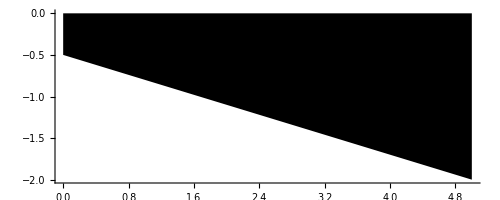

```mathematica
regArea = Region[reg, Axes-> True]
```

```mathematica
mesh1 = ToElementMesh[reg, "MeshElementType" -> TriangleElement, MaxCellMeasure ->r/(h2*1000) ]
```

ElementMesh[{{0.,5.},{-2.,0.}},{TriangleElement[<3939>]}]

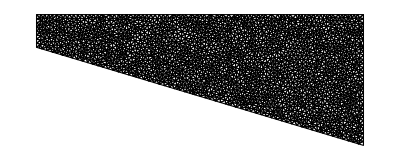

```mathematica
mesh1["Wireframe"]
```

```mathematica
PlaneStressOperator[u_,v_,EE_,ν_]:={({{0,-(EE ν)/(1-ν^2)},{-(EE (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-EE/(1-ν^2),0},{0,-(EE (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(EE (1-ν))/(2 (1-ν^2))},{-(EE ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(EE (1-ν))/(2 (1-ν^2)),0},{0,-EE/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
```

```mathematica
Dbc={DirichletCondition[v[x,y]==0,x==r && -h2 ≤ y ≤ 0],DirichletCondition[u[x,y]==0,x==r&& -h2 ≤ y ≤ 0]};
```

```mathematica
Sbc={0,NeumannValue[-q,y==0]};
```

```mathematica
{u1,v1}=NDSolveValue[{PlaneStressOperator[u,v,E1,ν1]==Sbc,Dbc},{u,v},{x,y}∈mesh1]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

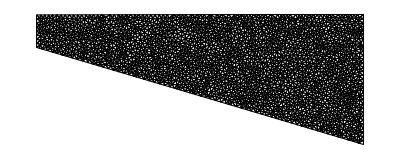

```mathematica
(* To visualize the deformed shape *)
ElementMeshDeformation[mesh1,{u1,v1}]["Wireframe"]
```

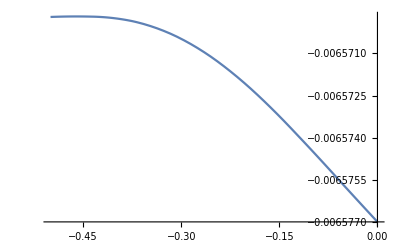

```mathematica
Plot[v1[0, y], {y, 0, -h1} ]
```

```mathematica
v1[0, -h1]
```

-0.0065697

```mathematica
Area[regArea]
```

6.25

```mathematica
val = If[-v1[0, -h1] > 0.01, "This exceeds a free end deflection of 0.01m", "Satisfactory"]
```

Satisfactory

### Computational Solution

```mathematica
(* generating a range of values between the given maximum and minimum *)
```

```mathematica
h1 = Range[0.01, 2.01, 0.1]
```

{0.01,0.11,0.21,0.31,0.41,0.51,0.61,0.71,0.81,0.91,1.01,1.11,1.21,1.31,1.41,1.51,1.61,1.71,1.81,1.91,2.01}

```mathematica
Dimensions[h1]
```

{21}

```mathematica
h2 = Range[2, 0.2, -0.1]
```

{2.,1.9,1.8,1.7,1.6,1.5,1.4,1.3,1.2,1.1,1.,0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2}

```mathematica
lessThan = {};
```

```mathematica
greaterThan = {};
```

```mathematica
LinearTaperedBeam[h1_, h2_] := (
For[i= 1, i < Dimensions[h1][[1]], i++, yEllipse = h2-h1[[i]];
(* Convex Geometry *)
reg = Polygon[{{0, 0}, {r, 0}, {r, -h2}, {0, -h1[[i]]}}];
Region[reg, Axes-> True];
mesh1 = ToElementMesh[reg, "MeshElementType" -> TriangleElement, MaxCellMeasure ->r/(h2*1000) ];
mesho =mesh1["Wireframe"];
Dbc={DirichletCondition[v[x,y]==0,x==r && -h2 ≤ y ≤ 0],DirichletCondition[u[x,y]==0,x==r&& -h2 ≤ y ≤ 0]};
Sbc={0,NeumannValue[-q,y==0]};
PlaneStressOperator[u_,v_,EE_,ν_]:={({{0,-(EE ν)/(1-ν^2)},{-(EE (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-EE/(1-ν^2),0},{0,-(EE (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(EE (1-ν))/(2 (1-ν^2))},{-(EE ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(EE (1-ν))/(2 (1-ν^2)),0},{0,-EE/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
{u1,v1}=NDSolveValue[{PlaneStressOperator[u,v,E1,ν1]==Sbc,Dbc},{u,v},{x,y}∈mesh1];
(* deflection at the free-end *)
(* To visualize the deformed shape *)
ElementMeshDeformation[mesh1,{u1,v1}]["Wireframe"];
Plot[v1[0, y], {y, 0, -h1[[i]]} ];
status = If[-v1[0, -h1[[i]]] > 0.01, "Greater than 0.01m", "Less than 0.01m"];
area = Area[reg];
If [-v1[0, -h1[[i]]] > 0.01, greaterThan=Append[greaterThan, area], lessThan=Append[lessThan, area]];
    Print["Linear Geometry", "\n", "\n", "h1: ",h1[[i]],"m,  ", "h2: ", h2, "m ", "\n","Free-End Deflection: ", -v1[0, -h1[[i]]] , "\n","Status: ", status,"\n","Area: ", area,"m^2  ", "\n", "\n", "--------------------------------------------------------------------------", "\n", "\n"];];
Return[];
)
```

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[1]]]]
```

Linear Geometry

h1: 0.01m,  h2: 2.m 
Free-End Deflection: 0.0127763
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 2.m 
Free-End Deflection: 0.0100604
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 2.m 
Free-End Deflection: 0.00870161
Status: Less than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 2.m 
Free-End Deflection: 0.00777318
Status: Less than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 2.m 
Free-End Deflection: 0.00707392
Status: Less than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 2.m 
Free-End Deflection: 0.00651923
Status: Less than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 2.m 
Free-End Deflection: 0.00606444
Status: Less than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 2.m 
Free-End Deflection: 0.00568251
Status: Less than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 2.m 
Free-End Deflection: 0.00535647
Status: Less than 0.01m
Area: 7.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 2.m 
Free-End Deflection: 0.00507424
Status: Less than 0.01m
Area: 7.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 2.m 
Free-End Deflection: 0.00482732
Status: Less than 0.01m
Area: 7.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 2.m 
Free-End Deflection: 0.00460941
Status: Less than 0.01m
Area: 7.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 2.m 
Free-End Deflection: 0.00441591
Status: Less than 0.01m
Area: 8.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 2.m 
Free-End Deflection: 0.00424295
Status: Less than 0.01m
Area: 8.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 2.m 
Free-End Deflection: 0.00408731
Status: Less than 0.01m
Area: 8.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 2.m 
Free-End Deflection: 0.00394671
Status: Less than 0.01m
Area: 8.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 2.m 
Free-End Deflection: 0.00381956
Status: Less than 0.01m
Area: 9.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 2.m 
Free-End Deflection: 0.00370396
Status: Less than 0.01m
Area: 9.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 2.m 
Free-End Deflection: 0.00359842
Status: Less than 0.01m
Area: 9.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 2.m 
Free-End Deflection: 0.00350189
Status: Less than 0.01m
Area: 9.775m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[2]]]]
```

Linear Geometry

h1: 0.01m,  h2: 1.9m 
Free-End Deflection: 0.0146764
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 1.9m 
Free-End Deflection: 0.0114692
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 1.9m 
Free-End Deflection: 0.00988352
Status: Less than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 1.9m 
Free-End Deflection: 0.00880667
Status: Less than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 1.9m 
Free-End Deflection: 0.00799922
Status: Less than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 1.9m 
Free-End Deflection: 0.00736077
Status: Less than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 1.9m 
Free-End Deflection: 0.00683866
Status: Less than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 1.9m 
Free-End Deflection: 0.00640155
Status: Less than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 1.9m 
Free-End Deflection: 0.00602884
Status: Less than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 1.9m 
Free-End Deflection: 0.0057069
Status: Less than 0.01m
Area: 7.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 1.9m 
Free-End Deflection: 0.00542586
Status: Less than 0.01m
Area: 7.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 1.9m 
Free-End Deflection: 0.00517822
Status: Less than 0.01m
Area: 7.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 1.9m 
Free-End Deflection: 0.00495833
Status: Less than 0.01m
Area: 7.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 1.9m 
Free-End Deflection: 0.00476205
Status: Less than 0.01m
Area: 8.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 1.9m 
Free-End Deflection: 0.00458581
Status: Less than 0.01m
Area: 8.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 1.9m 
Free-End Deflection: 0.00442697
Status: Less than 0.01m
Area: 8.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 1.9m 
Free-End Deflection: 0.00428271
Status: Less than 0.01m
Area: 8.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 1.9m 
Free-End Deflection: 0.00415231
Status: Less than 0.01m
Area: 9.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 1.9m 
Free-End Deflection: 0.00403325
Status: Less than 0.01m
Area: 9.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 1.9m 
Free-End Deflection: 0.0039244
Status: Less than 0.01m
Area: 9.525m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[3]]]]
```

Linear Geometry

h1: 0.01m,  h2: 1.8m 
Free-End Deflection: 0.0170057
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 1.8m 
Free-End Deflection: 0.0131808
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 1.8m 
Free-End Deflection: 0.0113137
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 1.8m 
Free-End Deflection: 0.0100537
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 1.8m 
Free-End Deflection: 0.0091135
Status: Less than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 1.8m 
Free-End Deflection: 0.00837258
Status: Less than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 1.8m 
Free-End Deflection: 0.00776845
Status: Less than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 1.8m 
Free-End Deflection: 0.00726382
Status: Less than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 1.8m 
Free-End Deflection: 0.0068347
Status: Less than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 1.8m 
Free-End Deflection: 0.00646458
Status: Less than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 1.8m 
Free-End Deflection: 0.006142
Status: Less than 0.01m
Area: 7.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 1.8m 
Free-End Deflection: 0.00585816
Status: Less than 0.01m
Area: 7.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 1.8m 
Free-End Deflection: 0.00560661
Status: Less than 0.01m
Area: 7.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 1.8m 
Free-End Deflection: 0.00538227
Status: Less than 0.01m
Area: 7.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 1.8m 
Free-End Deflection: 0.00518106
Status: Less than 0.01m
Area: 8.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 1.8m 
Free-End Deflection: 0.00499987
Status: Less than 0.01m
Area: 8.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 1.8m 
Free-End Deflection: 0.00483594
Status: Less than 0.01m
Area: 8.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 1.8m 
Free-End Deflection: 0.00468721
Status: Less than 0.01m
Area: 8.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 1.8m 
Free-End Deflection: 0.0045514
Status: Less than 0.01m
Area: 9.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 1.8m 
Free-End Deflection: 0.00442802
Status: Less than 0.01m
Area: 9.275m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[4]]]]
```

Linear Geometry

h1: 0.01m,  h2: 1.7m 
Free-End Deflection: 0.0198929
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 1.7m 
Free-End Deflection: 0.0152838
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 1.7m 
Free-End Deflection: 0.0130631
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 1.7m 
Free-End Deflection: 0.0115746
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 1.7m 
Free-End Deflection: 0.0104691
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 1.7m 
Free-End Deflection: 0.00960164
Status: Less than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 1.7m 
Free-End Deflection: 0.00889647
Status: Less than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 1.7m 
Free-End Deflection: 0.00830852
Status: Less than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 1.7m 
Free-End Deflection: 0.00781005
Status: Less than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 1.7m 
Free-End Deflection: 0.00738091
Status: Less than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 1.7m 
Free-End Deflection: 0.00700746
Status: Less than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 1.7m 
Free-End Deflection: 0.00667945
Status: Less than 0.01m
Area: 7.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 1.7m 
Free-End Deflection: 0.00638902
Status: Less than 0.01m
Area: 7.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 1.7m 
Free-End Deflection: 0.00613037
Status: Less than 0.01m
Area: 7.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 1.7m 
Free-End Deflection: 0.00589885
Status: Less than 0.01m
Area: 7.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 1.7m 
Free-End Deflection: 0.00569022
Status: Less than 0.01m
Area: 8.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 1.7m 
Free-End Deflection: 0.00550179
Status: Less than 0.01m
Area: 8.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 1.7m 
Free-End Deflection: 0.00533105
Status: Less than 0.01m
Area: 8.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 1.7m 
Free-End Deflection: 0.00517583
Status: Less than 0.01m
Area: 8.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 1.7m 
Free-End Deflection: 0.005034
Status: Less than 0.01m
Area: 9.025m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[5]]]]
```

Linear Geometry

h1: 0.01m,  h2: 1.6m 
Free-End Deflection: 0.0235226
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 1.6m 
Free-End Deflection: 0.0178983
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 1.6m 
Free-End Deflection: 0.0152276
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 1.6m 
Free-End Deflection: 0.0134508
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 1.6m 
Free-End Deflection: 0.0121378
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 1.6m 
Free-End Deflection: 0.0111113
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 1.6m 
Free-End Deflection: 0.0102795
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 1.6m 
Free-End Deflection: 0.00958856
Status: Less than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 1.6m 
Free-End Deflection: 0.00900356
Status: Less than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 1.6m 
Free-End Deflection: 0.00850113
Status: Less than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 1.6m 
Free-End Deflection: 0.00806452
Status: Less than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 1.6m 
Free-End Deflection: 0.00768184
Status: Less than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 1.6m 
Free-End Deflection: 0.00734351
Status: Less than 0.01m
Area: 7.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 1.6m 
Free-End Deflection: 0.00704257
Status: Less than 0.01m
Area: 7.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 1.6m 
Free-End Deflection: 0.00677342
Status: Less than 0.01m
Area: 7.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 1.6m 
Free-End Deflection: 0.0065311
Status: Less than 0.01m
Area: 7.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 1.6m 
Free-End Deflection: 0.00631299
Status: Less than 0.01m
Area: 8.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 1.6m 
Free-End Deflection: 0.00611474
Status: Less than 0.01m
Area: 8.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 1.6m 
Free-End Deflection: 0.00593478
Status: Less than 0.01m
Area: 8.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 1.6m 
Free-End Deflection: 0.00577068
Status: Less than 0.01m
Area: 8.775m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[6]]]]
```

Linear Geometry

h1: 0.01m,  h2: 1.5m 
Free-End Deflection: 0.0281505
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 1.5m 
Free-End Deflection: 0.0211941
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 1.5m 
Free-End Deflection: 0.0179422
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 1.5m 
Free-End Deflection: 0.0157954
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 1.5m 
Free-End Deflection: 0.0142178
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 1.5m 
Free-End Deflection: 0.0129895
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 1.5m 
Free-End Deflection: 0.0119976
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 1.5m 
Free-End Deflection: 0.0111763
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 1.5m 
Free-End Deflection: 0.0104821
Status: Greater than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 1.5m 
Free-End Deflection: 0.00988743
Status: Less than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 1.5m 
Free-End Deflection: 0.00937168
Status: Less than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 1.5m 
Free-End Deflection: 0.00892043
Status: Less than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 1.5m 
Free-End Deflection: 0.00852202
Status: Less than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 1.5m 
Free-End Deflection: 0.00816813
Status: Less than 0.01m
Area: 7.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 1.5m 
Free-End Deflection: 0.00785197
Status: Less than 0.01m
Area: 7.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 1.5m 
Free-End Deflection: 0.00756796
Status: Less than 0.01m
Area: 7.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 1.5m 
Free-End Deflection: 0.00731189
Status: Less than 0.01m
Area: 7.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 1.5m 
Free-End Deflection: 0.00707993
Status: Less than 0.01m
Area: 8.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 1.5m 
Free-End Deflection: 0.00686935
Status: Less than 0.01m
Area: 8.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 1.5m 
Free-End Deflection: 0.00667755
Status: Less than 0.01m
Area: 8.525m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[7]]]]
```

Linear Geometry

h1: 0.01m,  h2: 1.4m 
Free-End Deflection: 0.0341497
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 1.4m 
Free-End Deflection: 0.025413
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 1.4m 
Free-End Deflection: 0.0213976
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 1.4m 
Free-End Deflection: 0.0187688
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 1.4m 
Free-End Deflection: 0.0168477
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 1.4m 
Free-End Deflection: 0.0153595
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 1.4m 
Free-End Deflection: 0.0141618
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 1.4m 
Free-End Deflection: 0.0131725
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 1.4m 
Free-End Deflection: 0.0123394
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 1.4m 
Free-End Deflection: 0.0116269
Status: Greater than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 1.4m 
Free-End Deflection: 0.0110103
Status: Greater than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 1.4m 
Free-End Deflection: 0.0104716
Status: Greater than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 1.4m 
Free-End Deflection: 0.00999677
Status: Less than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 1.4m 
Free-End Deflection: 0.00957619
Status: Less than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 1.4m 
Free-End Deflection: 0.00920034
Status: Less than 0.01m
Area: 7.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 1.4m 
Free-End Deflection: 0.00886287
Status: Less than 0.01m
Area: 7.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 1.4m 
Free-End Deflection: 0.00855925
Status: Less than 0.01m
Area: 7.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 1.4m 
Free-End Deflection: 0.00828445
Status: Less than 0.01m
Area: 7.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 1.4m 
Free-End Deflection: 0.00803513
Status: Less than 0.01m
Area: 8.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 1.4m 
Free-End Deflection: 0.00780819
Status: Less than 0.01m
Area: 8.275m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[8]]]]
```

Linear Geometry

h1: 0.01m,  h2: 1.3m 
Free-End Deflection: 0.0420727
Status: Greater than 0.01m
Area: 3.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 1.3m 
Free-End Deflection: 0.0309095
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 1.3m 
Free-End Deflection: 0.0258711
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 1.3m 
Free-End Deflection: 0.0226012
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 1.3m 
Free-End Deflection: 0.0202292
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 1.3m 
Free-End Deflection: 0.0183987
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 1.3m 
Free-End Deflection: 0.0169314
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 1.3m 
Free-End Deflection: 0.0157244
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 1.3m 
Free-End Deflection: 0.014708
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 1.3m 
Free-End Deflection: 0.0138445
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 1.3m 
Free-End Deflection: 0.0130966
Status: Greater than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 1.3m 
Free-End Deflection: 0.0124452
Status: Greater than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 1.3m 
Free-End Deflection: 0.0118716
Status: Greater than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 1.3m 
Free-End Deflection: 0.0113642
Status: Greater than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 1.3m 
Free-End Deflection: 0.0109119
Status: Greater than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 1.3m 
Free-End Deflection: 0.010506
Status: Greater than 0.01m
Area: 7.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 1.3m 
Free-End Deflection: 0.0101399
Status: Greater than 0.01m
Area: 7.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 1.3m 
Free-End Deflection: 0.00980995
Status: Less than 0.01m
Area: 7.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 1.3m 
Free-End Deflection: 0.00951226
Status: Less than 0.01m
Area: 7.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 1.3m 
Free-End Deflection: 0.00924027
Status: Less than 0.01m
Area: 8.025m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[9]]]]
```

Linear Geometry

h1: 0.01m,  h2: 1.2m 
Free-End Deflection: 0.0527703
Status: Greater than 0.01m
Area: 3.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 1.2m 
Free-End Deflection: 0.0382144
Status: Greater than 0.01m
Area: 3.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 1.2m 
Free-End Deflection: 0.0317772
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 1.2m 
Free-End Deflection: 0.0276415
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 1.2m 
Free-End Deflection: 0.024658
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 1.2m 
Free-End Deflection: 0.0223685
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 1.2m 
Free-End Deflection: 0.0205432
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 1.2m 
Free-End Deflection: 0.0190447
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 1.2m 
Free-End Deflection: 0.0177895
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 1.2m 
Free-End Deflection: 0.0167224
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 1.2m 
Free-End Deflection: 0.0158014
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 1.2m 
Free-End Deflection: 0.0150012
Status: Greater than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 1.2m 
Free-End Deflection: 0.0142981
Status: Greater than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 1.2m 
Free-End Deflection: 0.0136753
Status: Greater than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 1.2m 
Free-End Deflection: 0.0131221
Status: Greater than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 1.2m 
Free-End Deflection: 0.0126276
Status: Greater than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 1.2m 
Free-End Deflection: 0.0121816
Status: Greater than 0.01m
Area: 7.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 1.2m 
Free-End Deflection: 0.01178
Status: Greater than 0.01m
Area: 7.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 1.2m 
Free-End Deflection: 0.0114165
Status: Greater than 0.01m
Area: 7.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 1.2m 
Free-End Deflection: 0.0110847
Status: Greater than 0.01m
Area: 7.775m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[10]]]]
```

Linear Geometry

h1: 0.01m,  h2: 1.1m 
Free-End Deflection: 0.0675832
Status: Greater than 0.01m
Area: 2.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 1.1m 
Free-End Deflection: 0.0481567
Status: Greater than 0.01m
Area: 3.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 1.1m 
Free-End Deflection: 0.0397541
Status: Greater than 0.01m
Area: 3.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 1.1m 
Free-End Deflection: 0.0344123
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 1.1m 
Free-End Deflection: 0.0305893
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 1.1m 
Free-End Deflection: 0.0276704
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 1.1m 
Free-End Deflection: 0.0253528
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 1.1m 
Free-End Deflection: 0.0234589
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 1.1m 
Free-End Deflection: 0.0218772
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 1.1m 
Free-End Deflection: 0.020537
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 1.1m 
Free-End Deflection: 0.0193841
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 1.1m 
Free-End Deflection: 0.0183818
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 1.1m 
Free-End Deflection: 0.0175036
Status: Greater than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 1.1m 
Free-End Deflection: 0.0167282
Status: Greater than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 1.1m 
Free-End Deflection: 0.0160393
Status: Greater than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 1.1m 
Free-End Deflection: 0.0154237
Status: Greater than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 1.1m 
Free-End Deflection: 0.0148684
Status: Greater than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 1.1m 
Free-End Deflection: 0.0143693
Status: Greater than 0.01m
Area: 7.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 1.1m 
Free-End Deflection: 0.0139195
Status: Greater than 0.01m
Area: 7.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 1.1m 
Free-End Deflection: 0.0135091
Status: Greater than 0.01m
Area: 7.525m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[11]]]]
```

Linear Geometry

h1: 0.01m,  h2: 1.m 
Free-End Deflection: 0.0887183
Status: Greater than 0.01m
Area: 2.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 1.m 
Free-End Deflection: 0.0620663
Status: Greater than 0.01m
Area: 2.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 1.m 
Free-End Deflection: 0.050816
Status: Greater than 0.01m
Area: 3.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 1.m 
Free-End Deflection: 0.0437516
Status: Greater than 0.01m
Area: 3.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 1.m 
Free-End Deflection: 0.0387367
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 1.m 
Free-End Deflection: 0.0349331
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 1.m 
Free-End Deflection: 0.0319274
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 1.m 
Free-End Deflection: 0.0294782
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 1.m 
Free-End Deflection: 0.0274444
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 1.m 
Free-End Deflection: 0.0257206
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 1.m 
Free-End Deflection: 0.0242451
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 1.m 
Free-End Deflection: 0.0229632
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 1.m 
Free-End Deflection: 0.0218428
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 1.m 
Free-End Deflection: 0.0208574
Status: Greater than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 1.m 
Free-End Deflection: 0.0199817
Status: Greater than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 1.m 
Free-End Deflection: 0.0192001
Status: Greater than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 1.m 
Free-End Deflection: 0.0184974
Status: Greater than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 1.m 
Free-End Deflection: 0.0178665
Status: Greater than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 1.m 
Free-End Deflection: 0.0172973
Status: Greater than 0.01m
Area: 7.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 1.m 
Free-End Deflection: 0.0167788
Status: Greater than 0.01m
Area: 7.275m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[12]]]]
```

Linear Geometry

h1: 0.01m,  h2: 0.9m 
Free-End Deflection: 0.119985
Status: Greater than 0.01m
Area: 2.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 0.9m 
Free-End Deflection: 0.0821758
Status: Greater than 0.01m
Area: 2.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 0.9m 
Free-End Deflection: 0.0666607
Status: Greater than 0.01m
Area: 2.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 0.9m 
Free-End Deflection: 0.0570465
Status: Greater than 0.01m
Area: 3.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 0.9m 
Free-End Deflection: 0.0502781
Status: Greater than 0.01m
Area: 3.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 0.9m 
Free-End Deflection: 0.0451867
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 0.9m 
Free-End Deflection: 0.0411832
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 0.9m 
Free-End Deflection: 0.0379368
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 0.9m 
Free-End Deflection: 0.0352427
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 0.9m 
Free-End Deflection: 0.0329684
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 0.9m 
Free-End Deflection: 0.031038
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 0.9m 
Free-End Deflection: 0.0293588
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 0.9m 
Free-End Deflection: 0.0278942
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 0.9m 
Free-End Deflection: 0.0266067
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 0.9m 
Free-End Deflection: 0.0254657
Status: Greater than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 0.9m 
Free-End Deflection: 0.0244464
Status: Greater than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 0.9m 
Free-End Deflection: 0.0235355
Status: Greater than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 0.9m 
Free-End Deflection: 0.0227161
Status: Greater than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 0.9m 
Free-End Deflection: 0.0219802
Status: Greater than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 0.9m 
Free-End Deflection: 0.0213093
Status: Greater than 0.01m
Area: 7.025m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[13]]]]
```

Linear Geometry

h1: 0.01m,  h2: 0.8m 
Free-End Deflection: 0.168274
Status: Greater than 0.01m
Area: 2.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 0.8m 
Free-End Deflection: 0.112432
Status: Greater than 0.01m
Area: 2.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 0.8m 
Free-End Deflection: 0.0902459
Status: Greater than 0.01m
Area: 2.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 0.8m 
Free-End Deflection: 0.0766929
Status: Greater than 0.01m
Area: 2.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 0.8m 
Free-End Deflection: 0.0672561
Status: Greater than 0.01m
Area: 3.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 0.8m 
Free-End Deflection: 0.0602066
Status: Greater than 0.01m
Area: 3.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 0.8m 
Free-End Deflection: 0.0546973
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 0.8m 
Free-End Deflection: 0.050253
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 0.8m 
Free-End Deflection: 0.0465774
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 0.8m 
Free-End Deflection: 0.0434969
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 0.8m 
Free-End Deflection: 0.0408688
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 0.8m 
Free-End Deflection: 0.038602
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 0.8m 
Free-End Deflection: 0.0366277
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 0.8m 
Free-End Deflection: 0.034894
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 0.8m 
Free-End Deflection: 0.0333609
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 0.8m 
Free-End Deflection: 0.0319968
Status: Greater than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 0.8m 
Free-End Deflection: 0.0307765
Status: Greater than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 0.8m 
Free-End Deflection: 0.0296797
Status: Greater than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 0.8m 
Free-End Deflection: 0.0286898
Status: Greater than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 0.8m 
Free-End Deflection: 0.0277929
Status: Greater than 0.01m
Area: 6.775m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[14]]]]
```

Linear Geometry

h1: 0.01m,  h2: 0.7m 
Free-End Deflection: 0.24712
Status: Greater than 0.01m
Area: 1.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 0.7m 
Free-End Deflection: 0.160323
Status: Greater than 0.01m
Area: 2.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 0.7m 
Free-End Deflection: 0.127086
Status: Greater than 0.01m
Area: 2.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 0.7m 
Free-End Deflection: 0.107156
Status: Greater than 0.01m
Area: 2.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 0.7m 
Free-End Deflection: 0.0934303
Status: Greater than 0.01m
Area: 2.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 0.7m 
Free-End Deflection: 0.0832547
Status: Greater than 0.01m
Area: 3.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 0.7m 
Free-End Deflection: 0.0753639
Status: Greater than 0.01m
Area: 3.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 0.7m 
Free-End Deflection: 0.0690285
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 0.7m 
Free-End Deflection: 0.0638181
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 0.7m 
Free-End Deflection: 0.0594641
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 0.7m 
Free-End Deflection: 0.0557754
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 0.7m 
Free-End Deflection: 0.052581
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 0.7m 
Free-End Deflection: 0.0498309
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 0.7m 
Free-End Deflection: 0.0474001
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 0.7m 
Free-End Deflection: 0.0452645
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 0.7m 
Free-End Deflection: 0.0433677
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 0.7m 
Free-End Deflection: 0.0416738
Status: Greater than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 0.7m 
Free-End Deflection: 0.0401502
Status: Greater than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 0.7m 
Free-End Deflection: 0.0387864
Status: Greater than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 0.7m 
Free-End Deflection: 0.0375471
Status: Greater than 0.01m
Area: 6.525m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[15]]]]
```

Linear Geometry

h1: 0.01m,  h2: 0.6m 
Free-End Deflection: 0.385265
Status: Greater than 0.01m
Area: 1.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 0.6m 
Free-End Deflection: 0.241126
Status: Greater than 0.01m
Area: 1.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 0.6m 
Free-End Deflection: 0.188346
Status: Greater than 0.01m
Area: 2.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 0.6m 
Free-End Deflection: 0.157316
Status: Greater than 0.01m
Area: 2.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 0.6m 
Free-End Deflection: 0.136233
Status: Greater than 0.01m
Area: 2.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 0.6m 
Free-End Deflection: 0.120772
Status: Greater than 0.01m
Area: 2.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 0.6m 
Free-End Deflection: 0.10887
Status: Greater than 0.01m
Area: 3.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 0.6m 
Free-End Deflection: 0.0993757
Status: Greater than 0.01m
Area: 3.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 0.6m 
Free-End Deflection: 0.0916024
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 0.6m 
Free-End Deflection: 0.0851268
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 0.6m 
Free-End Deflection: 0.0796865
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 0.6m 
Free-End Deflection: 0.0749907
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 0.6m 
Free-End Deflection: 0.0709109
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 0.6m 
Free-End Deflection: 0.0673612
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 0.6m 
Free-End Deflection: 0.064261
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 0.6m 
Free-End Deflection: 0.0614721
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 0.6m 
Free-End Deflection: 0.0590275
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 0.6m 
Free-End Deflection: 0.0568038
Status: Greater than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 0.6m 
Free-End Deflection: 0.0547697
Status: Greater than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 0.6m 
Free-End Deflection: 0.0530164
Status: Greater than 0.01m
Area: 6.275m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[16]]]]
```

Linear Geometry

h1: 0.01m,  h2: 0.5m 
Free-End Deflection: 0.651268
Status: Greater than 0.01m
Area: 1.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 0.5m 
Free-End Deflection: 0.389612
Status: Greater than 0.01m
Area: 1.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 0.5m 
Free-End Deflection: 0.298978
Status: Greater than 0.01m
Area: 1.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 0.5m 
Free-End Deflection: 0.246936
Status: Greater than 0.01m
Area: 2.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 0.5m 
Free-End Deflection: 0.212126
Status: Greater than 0.01m
Area: 2.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 0.5m 
Free-End Deflection: 0.186877
Status: Greater than 0.01m
Area: 2.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 0.5m 
Free-End Deflection: 0.167592
Status: Greater than 0.01m
Area: 2.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 0.5m 
Free-End Deflection: 0.152336
Status: Greater than 0.01m
Area: 3.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 0.5m 
Free-End Deflection: 0.139954
Status: Greater than 0.01m
Area: 3.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 0.5m 
Free-End Deflection: 0.12969
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 0.5m 
Free-End Deflection: 0.121044
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 0.5m 
Free-End Deflection: 0.113705
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 0.5m 
Free-End Deflection: 0.10732
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 0.5m 
Free-End Deflection: 0.101767
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 0.5m 
Free-End Deflection: 0.0968912
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 0.5m 
Free-End Deflection: 0.092579
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 0.5m 
Free-End Deflection: 0.0887421
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 0.5m 
Free-End Deflection: 0.0853096
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 0.5m 
Free-End Deflection: 0.0822759
Status: Greater than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 0.5m 
Free-End Deflection: 0.0794955
Status: Greater than 0.01m
Area: 6.025m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[17]]]]
```

Linear Geometry

h1: 0.01m,  h2: 0.4m 
Free-End Deflection: 1.23653
Status: Greater than 0.01m
Area: 1.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 0.4m 
Free-End Deflection: 0.697392
Status: Greater than 0.01m
Area: 1.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 0.4m 
Free-End Deflection: 0.523259
Status: Greater than 0.01m
Area: 1.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 0.4m 
Free-End Deflection: 0.426242
Status: Greater than 0.01m
Area: 1.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 0.4m 
Free-End Deflection: 0.362411
Status: Greater than 0.01m
Area: 2.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 0.4m 
Free-End Deflection: 0.316932
Status: Greater than 0.01m
Area: 2.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 0.4m 
Free-End Deflection: 0.282518
Status: Greater than 0.01m
Area: 2.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 0.4m 
Free-End Deflection: 0.255549
Status: Greater than 0.01m
Area: 2.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 0.4m 
Free-End Deflection: 0.233833
Status: Greater than 0.01m
Area: 3.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 0.4m 
Free-End Deflection: 0.215908
Status: Greater than 0.01m
Area: 3.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 0.4m 
Free-End Deflection: 0.200883
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 0.4m 
Free-End Deflection: 0.188081
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 0.4m 
Free-End Deflection: 0.17709
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 0.4m 
Free-End Deflection: 0.167541
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 0.4m 
Free-End Deflection: 0.159203
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 0.4m 
Free-End Deflection: 0.151802
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 0.4m 
Free-End Deflection: 0.14528
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 0.4m 
Free-End Deflection: 0.139427
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 0.4m 
Free-End Deflection: 0.134308
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 0.4m 
Free-End Deflection: 0.129582
Status: Greater than 0.01m
Area: 5.775m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[18]]]]
```

Linear Geometry

h1: 0.01m,  h2: 0.3m 
Free-End Deflection: 2.81655
Status: Greater than 0.01m
Area: 0.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 0.3m 
Free-End Deflection: 1.46321
Status: Greater than 0.01m
Area: 1.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 0.3m 
Free-End Deflection: 1.06562
Status: Greater than 0.01m
Area: 1.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 0.3m 
Free-End Deflection: 0.852275
Status: Greater than 0.01m
Area: 1.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 0.3m 
Free-End Deflection: 0.715758
Status: Greater than 0.01m
Area: 1.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 0.3m 
Free-End Deflection: 0.620184
Status: Greater than 0.01m
Area: 2.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 0.3m 
Free-End Deflection: 0.548731
Status: Greater than 0.01m
Area: 2.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 0.3m 
Free-End Deflection: 0.493057
Status: Greater than 0.01m
Area: 2.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 0.3m 
Free-End Deflection: 0.448743
Status: Greater than 0.01m
Area: 2.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 0.3m 
Free-End Deflection: 0.412472
Status: Greater than 0.01m
Area: 3.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 0.3m 
Free-End Deflection: 0.382465
Status: Greater than 0.01m
Area: 3.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 0.3m 
Free-End Deflection: 0.35663
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 0.3m 
Free-End Deflection: 0.335298
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 0.3m 
Free-End Deflection: 0.316394
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 0.3m 
Free-End Deflection: 0.299915
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 0.3m 
Free-End Deflection: 0.285402
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 0.3m 
Free-End Deflection: 0.272553
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 0.3m 
Free-End Deflection: 0.261108
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 0.3m 
Free-End Deflection: 0.25085
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 0.3m 
Free-End Deflection: 0.241604
Status: Greater than 0.01m
Area: 5.525m^2  

--------------------------------------------------------------------------

```mathematica
For[i= 1, i < Dimensions[h2][[1]], i++, LinearTaperedBeam[h1, h2[[19]]]]
```

Linear Geometry

h1: 0.01m,  h2: 0.2m 
Free-End Deflection: 8.89305
Status: Greater than 0.01m
Area: 0.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.11m,  h2: 0.2m 
Free-End Deflection: 4.06784
Status: Greater than 0.01m
Area: 0.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.21m,  h2: 0.2m 
Free-End Deflection: 2.8404
Status: Greater than 0.01m
Area: 1.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.31m,  h2: 0.2m 
Free-End Deflection: 2.21594
Status: Greater than 0.01m
Area: 1.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.41m,  h2: 0.2m 
Free-End Deflection: 1.82573
Status: Greater than 0.01m
Area: 1.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.51m,  h2: 0.2m 
Free-End Deflection: 1.55953
Status: Greater than 0.01m
Area: 1.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.61m,  h2: 0.2m 
Free-End Deflection: 1.36802
Status: Greater than 0.01m
Area: 2.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.71m,  h2: 0.2m 
Free-End Deflection: 1.21532
Status: Greater than 0.01m
Area: 2.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.81m,  h2: 0.2m 
Free-End Deflection: 1.09824
Status: Greater than 0.01m
Area: 2.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 0.91m,  h2: 0.2m 
Free-End Deflection: 1.00223
Status: Greater than 0.01m
Area: 2.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.01m,  h2: 0.2m 
Free-End Deflection: 0.922521
Status: Greater than 0.01m
Area: 3.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.11m,  h2: 0.2m 
Free-End Deflection: 0.855328
Status: Greater than 0.01m
Area: 3.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.21m,  h2: 0.2m 
Free-End Deflection: 0.803822
Status: Greater than 0.01m
Area: 3.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.31m,  h2: 0.2m 
Free-End Deflection: 0.759141
Status: Greater than 0.01m
Area: 3.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.41m,  h2: 0.2m 
Free-End Deflection: 0.70244
Status: Greater than 0.01m
Area: 4.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.51m,  h2: 0.2m 
Free-End Deflection: 0.67991
Status: Greater than 0.01m
Area: 4.275m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.61m,  h2: 0.2m 
Free-End Deflection: 0.647253
Status: Greater than 0.01m
Area: 4.525m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.71m,  h2: 0.2m 
Free-End Deflection: 0.618182
Status: Greater than 0.01m
Area: 4.775m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.81m,  h2: 0.2m 
Free-End Deflection: 0.592371
Status: Greater than 0.01m
Area: 5.025m^2  

--------------------------------------------------------------------------

Linear Geometry

h1: 1.91m,  h2: 0.2m 
Free-End Deflection: 0.569019
Status: Greater than 0.01m
Area: 5.275m^2  

--------------------------------------------------------------------------

```mathematica
lessThan
```

{5.525,5.775,6.025,6.275,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,8.525,8.775,9.025,9.275,9.525,9.775,5.275,5.525,5.775,6.025,6.275,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,8.525,8.775,9.025,9.275,9.525,5.525,5.775,6.025,6.275,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,8.525,8.775,9.025,9.275,5.525,5.775,6.025,6.275,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,8.525,8.775,9.025,5.775,6.025,6.275,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,8.525,8.775,6.025,6.275,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,8.525,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,7.525,7.775,8.025}

```mathematica
digitLessThan=Select[lessThan,NumericQ[#]&&!IntegerQ[#]&]
```

{5.525,5.775,6.025,6.275,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,8.525,8.775,9.025,9.275,9.525,9.775,5.275,5.525,5.775,6.025,6.275,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,8.525,8.775,9.025,9.275,9.525,5.525,5.775,6.025,6.275,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,8.525,8.775,9.025,9.275,5.525,5.775,6.025,6.275,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,8.525,8.775,9.025,5.775,6.025,6.275,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,8.525,8.775,6.025,6.275,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,8.525,6.525,6.775,7.025,7.275,7.525,7.775,8.025,8.275,7.525,7.775,8.025}

```mathematica
Print["The smallest Area is:", Min[digitLessThan], "m^2."]
```

The smallest Area is:5.275m^2.

### Therefore, the smallest area we obtained for the Tapered beam is 5.275 m^2.

## Concave Taperness (Some Additional formulation)

Practicing different geometries.

### Simple Example Program

```mathematica
ClearAll["Global`*"]
```

```mathematica
E1 = 40*10^9; ν1 = 0.3;
q = 1*10^6;  (* in MPa *)
h1 = 0.5; h2 = 2;
```

```mathematica
L=5;h2=2;ry=2;
```

```mathematica
r=5;
```

```mathematica
(* ellipse equation *)
```

```mathematica
rxx=.;
sol1=NSolve[(x-0)^2/rxx^2+((yy-0)/ry^2)^2-1==0/.{yy->.5,x->-5},rxx]//N
```

{{rxx→5.03953},{rxx→-5.03953}}

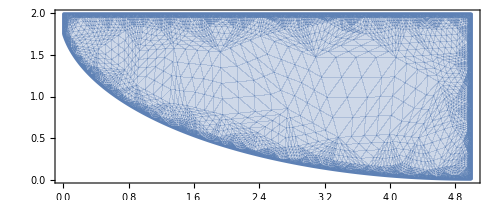

```mathematica
rx=5.03953;
concaveBeam=RegionDifference[Rectangle[{0,0},{L,h2}],RegionDifference[Rectangle[{0,0},{L,h2}],RegionUnion[Disk[{L,h2},{rx,ry}]]]];
Region[%,Axes-> True];RegionPlot[%,AspectRatio-> True]
```

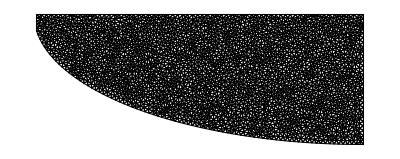

```mathematica
mesh2 = ToElementMesh[concaveBeam, MaxCellMeasure -> r/(h2*1000.)];
mesho= mesh2["Wireframe"]
```

```mathematica
Dbc={DirichletCondition[v[x,y]==0,x==r && 0 ≤ y ≤ h2],DirichletCondition[u[x,y]==0,x==r&& 0≤y≤h2]};
Sbc={0,NeumannValue[-q,y==h2]};
```

```mathematica
PlaneStressOperator[u_,v_,EE_,ν_]:={({{0,-(EE ν)/(1-ν^2)},{-(EE (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-EE/(1-ν^2),0},{0,-(EE (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(EE (1-ν))/(2 (1-ν^2))},{-(EE ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(EE (1-ν))/(2 (1-ν^2)),0},{0,-EE/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
```

```mathematica
{u1,v1}=NDSolveValue[{PlaneStressOperator[u,v,E1,ν1]==Sbc,Dbc},{u,v},{x,y}∈mesh2]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

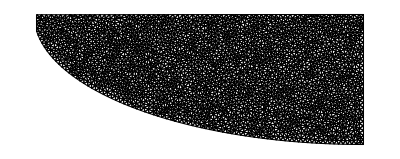

```mathematica
(* To visualize the deformed shape *)
ElementMeshDeformation[mesh2,{u1,v1}]["Wireframe"]
```

```mathematica
v1[0, h2]
```

-0.00392123

```mathematica
status = If[-v1[0, h2] > 0.01, "Greater than 0.01m", "Less than 0.01m"]
```

Less than 0.01m

## Basic Structural Mechanics Solution of the desired shape

## Basic Structural Mechanics Solution

```mathematica
ClearAll["Global`*"]
```

```mathematica
hx = h1 + (h2-h1) x /L
```

h1+((-h1+h2) x)/L

```mathematica
Mx = (q x^2)/2
```

(q x^2)/2

```mathematica
II = (hx)^3/12
```

1/12 (h1+((-h1+h2) x)/L)^3

```mathematica
s = Integrate[Mx/EE, x] + C1
```

C1+(q x^3)/(6 EE)

```mathematica
v = Integrate[s, x] + C2
```

C2+C1 x+(q x^4)/(24 EE)

```mathematica
vx = D[v, x]
```

C1+(q x^3)/(6 EE)

```mathematica
bc1 = vx == 0  /. x -> L
```

C1+(L^3 q)/(6 EE)==0

```mathematica
bc2 = v == 0 /. x -> L
```

C2+C1 L+(L^4 q)/(24 EE)==0

```mathematica
sol = Solve[{bc1, bc2}, {C1, C2}]
```

{{C1→-(L^3 q)/(6 EE),C2→(L^4 q)/(8 EE)}}

```mathematica
v = Simplify[v /. sol[[1]]]
```

(q (3 L^4-4 L^3 x+x^4))/(24 EE)

```mathematica
v /. {q -> 1*10^6, EE -> 40*10^9, x-> 0, L -> 5.}
```

0.00195313

Deflection of the beam computed analytically.

### Finite Element Solution

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<NDSolve`FEM`
```

```mathematica
E1 = 40*10^9; ν1 = 0.3;
```

```mathematica
q = 1*10^6;  (* in MPa *)
```

```mathematica
(* Assumed values of h1 and h2 *)
```

```mathematica
h1 = 0.21; h2 = 1.9;
```

```mathematica
r =5;
```

```mathematica
yEllipse = h2-h1;
```

```mathematica
a1 = Rectangle[{0, 0}, {r, h2}]
```

Rectangle[{0,0},{5,1.9}]

```mathematica
a2 = Disk[{0, 0}, {r, yEllipse}]
```

Disk[{0,0},{5,1.69}]

```mathematica
taper = RegionDifference[a1, a2]
```

BooleanRegion[#1&&!#2&,{Rectangle[{0,0},{5,1.9}],Disk[{0,0},{5,1.69}]}]

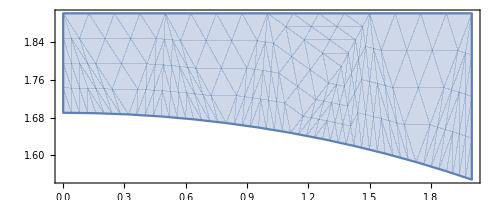

```mathematica
RegionPlot[taper, AspectRatio-> True]
```

```mathematica
r/(h2*1000.)
```

0.00263158

```mathematica
mesh1 = ToElementMesh[taper, MaxCellMeasure -> r/(h2*1000.)]
```

ElementMesh[{{0.,5.},{0.,1.9}},{TriangleElement[<1729>]}]

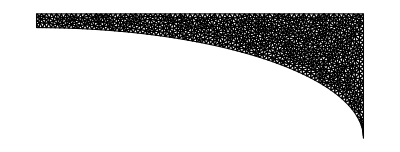

```mathematica
mesh1["Wireframe"]
```

```mathematica
PlaneStressOperator[u_,v_,EE_,ν_]:={({{0,-(EE ν)/(1-ν^2)},{-(EE (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-EE/(1-ν^2),0},{0,-(EE (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(EE (1-ν))/(2 (1-ν^2))},{-(EE ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(EE (1-ν))/(2 (1-ν^2)),0},{0,-EE/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
```

```mathematica
Dbc={DirichletCondition[v[x,y]==0,x==r && 0 ≤ y ≤ h2],DirichletCondition[u[x,y]==0,x==r&& 0≤y≤h2]};
```

```mathematica
Sbc={0,NeumannValue[-q,y==h2]};
```

```mathematica
{u1,v1}=NDSolveValue[{PlaneStressOperator[u,v,E1,ν1]==Sbc,Dbc},{u,v},{x,y}∈mesh1]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

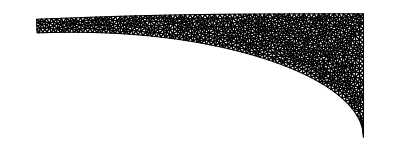

```mathematica
(* To visualize the deformed shape *)
ElementMeshDeformation[mesh1,{u1,v1}]["Wireframe"]
```

```mathematica
v1[0, h2]  (* This exceeds a free end deflection of 0.01m *)
```

-0.0842456

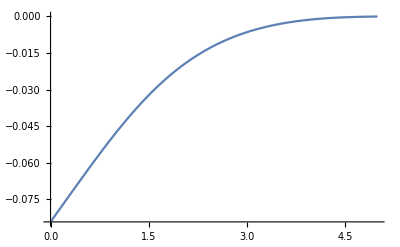

```mathematica
Plot[v1[x, h2], {x, 0, r}, PlotRange->Full]
```

## Observations

We believe that utilizing the speed and resources of a modern computer is the most reasonable way of approaching such an open ended-question. We also observe that the value we obtained is very close to the minimum (that is if a minimum below ours does exist) due to several reasons. Our optimum area value is at the border in between area values that yield a deflection less than 0.01m and above 0.01m. In fact, we found several geometries (with different curves of course) that yielded values the same area as 5.275 m^2 but with a free-end deflection exactly equal to 0.01m or slightly above it. Examples of such a geometry is shown below:

So this confirms that our obtained value of minimum area 5.275 m^2 is the optimum area for the tapered beam Possible.

Cross-section of Beam

```mathematica
mesh1["Wireframe"]
```

-Graphics-

## Group Members Contribution

1, Faisal Lawan Muhammad (g202210460): Developed core algorithm for optimal area search while  converting the individual examples solved by other team members into the loop driven optimal area searching functions (e.g LinearTaperedBeam, ConvexTaperedBeam). Program optimization and design to ensure that compute space (RAM) on computer is efficiently utilized when running the program. Played with various geometries while trying to reach the optimum Area. Debugging of Mathematica code and writhing of introduction and observation sections.